# Explore and Process FBA Kernel Solutionspace

#### Copyright

© Copyright 2022 Wynand Verwoerd

This file is part of SSKernel.

The SSKernel program is free software; you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation; either version 3 of the License, or (at your option) any later version . 
This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE . See the GNU General Public License for more details . 
You should have received a copy of the GNU General Public License along with this program . If not, see http://www.gnu.org/licenses/

#### Summary

This file is meant to demonstrate how to load and analyze the output file from a SSKernel calculation that has been performed previously. It can be used as a template that can be expanded for further calculations and analysis.

It is selfcontained, not using any of the program code in the Packages directory, and defines the special datastructures found in the SSKernel output files and a few utilities to manipulate them in the first section below.

### Utility functions

Data structures to specify solution spaces

```mathematica
(*SOLUTION SPACE DATA STRUCTURES*)(*The following lines define names for components of solution and Kernel spaces to facilitate calling of functions that use them.

NOTE:Do not assign values to these names,or use them in fuctions that change their arguments i.e.,have HoldFirst,HoldAll etc.attributes,as that will freeze them to fixed values.*)

(*Reduced space containing solutions to stoichiometry and objective constraints,after removing fixed fluxes,prismatic rays and linealities*)
SolutionSpace={{},{}};
SScons:=SolutionSpace[[1,1]];SSvals:=SolutionSpace[[1,2]];
SSTransform:=SolutionSpace[[2]];(*Affine transform from FS to RSS*)
SSOrigin:=SolutionSpace[[2,1]];SSBasis:=SolutionSpace[[2,2]];

(*Bounded Kernel solution space after coincidence and tangent capping*)
KernelSpace={{},{}};
Kernelcons:=KernelSpace[[1,1]];Kernelvals:=KernelSpace[[1,2]];
KernelTransform:=KernelSpace[[2]];(*Affine transform from FS to CSS*)
KernelOrigin:=KernelSpace[[2,1]];KernelBasis:=KernelSpace[[2,2]];
```

Transfer flux vectors and constraint sets between spaces using their SS specifications, e.g. between the full flux space and the Kernel solution space:

```mathematica
UpliftPoint[Lopoint_,transform_]:=Module[{pointset},pointset=If[VectorQ[Lopoint],{Lopoint},Lopoint];
pointset=Map[Chop[#.transform[[2]]+transform[[1]],0.0001]&,pointset];
If[VectorQ[Lopoint],pointset[[1]],pointset]]
DowncastPoint[Hipoint_,transform_]:=Module[{pointset},pointset=If[VectorQ[Hipoint],{Hipoint},Hipoint];
pointset=Map[Chop[(#-transform[[1]]).Transpose[transform[[2]]],0.0001]&,pointset];
If[VectorQ[Hipoint],pointset[[1]],pointset]]

CombineTransform[HighToMedium_,MediumToLow_]:=Block[{hidim,middim,lodim,HMdims,MLdims},hidim=Length[HighToMedium[[1]]];
middim=Length[MediumToLow[[1]]];
HMdims=Dimensions[HighToMedium[[2]]];
MLdims=Dimensions[MediumToLow[[2]]];
lodim=MLdims[[1]];
If[MLdims=={lodim,middim}&&HMdims=={middim,hidim},{HighToMedium[[1]]+MediumToLow[[1]].HighToMedium[[2]],MediumToLow[[2]].HighToMedium[[2]]},Print["Dimensions of transforms are incompatible!"];{}]]

DowncastConstraints[convecs_,convals_,transform_]:=Module[{bt,norms,keepers,projects,newvecs,newvals,tol=0.001},(*Constraint vectors with projection on the subspace less than tol,are omitted.Such a vector generally produces a constraint hyperplane cutoff on the subspace,at a distance (conval/projection).If the projection is zero,the intercept is at Infinity,and so for small projections its value is very sensitive to numerical error,but normally falls beyond the cutoffs of other constraints.That means it becomes redundant and would anyway be eliminated by redundancy trimming performed after the downcast,so it is more efficient to eliminate it here.More seriously,in cases where the corresponding conval values is small (i.e.,the coordinate origin is on or near the polytope periphery) the cutoff it produces can be within the range of other constraint hyperplanes,but spurious because of numerical inaccuracy in the direction of the vector.Generally,the accuracy of a downcast/uplift cycle is found to be about 10-5 to 10^-6. So choose tol well bigger than this,e.g.10^-3 so constraints that are kept have reliable cutoffs.Conceivably,this may cause the downcasted polytope to be open since it misses some constraint,but such cases have not be observed yet.The alternative is worse,cases have arisen where a downcasted constraint set excluded the current interior origin or became completely infeasible.*)bt=Transpose[transform[[2]]];
projects=convecs.bt;norms=Norm/@projects;
keepers=Map[If[#>tol,True,False]&,norms];
(*Print[{"Keepers",keepers,"Norms",norms}];*)norms=Pick[norms,keepers];
newvecs=Pick[projects,keepers]/norms;
newvals=Pick[convals,keepers];
(*Print[{"newvals",newvals}];
Print[{"Dot",Pick[convecs,keepers].transform[[1]]}];*)newvals=Chop[(newvals-Pick[convecs,keepers].transform[[1]])/norms,0.0001];
{newvecs,newvals}]


UpliftConstraints[convecs_,convals_,transform_]:=Module[{projects,newvals},projects=convecs.transform[[2]];
newvals=convals+projects.transform[[1]];
{projects,Chop[newvals,0.0001]}]

SolutionTest[flux_,solutionspace_,tol_: 0.001]:=Module[{osflux,slacks,satisfy,truncate},osflux=DowncastPoint[flux,solutionspace[[2]]];
slacks=Chop[solutionspace[[1,2]]-solutionspace[[1,1]].osflux,tol];
(*Print[slacks];*)satisfy=Min[slacks]>-tol;
truncate=Norm[UpliftPoint[osflux,solutionspace[[2]]]-flux]>tol;
Which[satisfy&&!truncate,"Full vector in solution space",satisfy,"Projected vector in solution space",True,"Vector violates constraints by "<>TextString[Min[0,#]&/@slacks]]]
```

Given a polytope specified by the constraints matrix Amat and values vector bvec, the following function finds the radii through the origin (interior to the polytope) to the intercepts along the direction of the vector supplied as a 3rd argument. A pair of radii is delivered, the positive value is in the forward direction of the supplied vector, and the negative value is backward.

```mathematica
(*Using Compile makes the function faster by a factor 10 to 20*)Radii=Compile[{{Amat,_Real,2},{bvec,_Real,1},{vector,_Real,1}},Module[{Avec={1.},norm=0.,rad1=0.,rad2=0.,Infinity=10.^10,tol=0.00001},If[Min[bvec]<-tol,Print[Style["Radii not calculated because origin is not interior by margin "<>TextString[Min[bvec]],Red]];Abort[];
Return[{0.,0.}]];
norm=Norm[vector];
If[norm<tol,Print[Style["Radii not calculated, because the vector of length "<>TextString[norm]<>" has an amnbiguous direction!",Red]];Abort[];
Return[{0.,0.}]];
(*Avec consists of the components of all constraint plane normals,along vector*)(*For the compiler,dot product needs two matrices.And change the result back to a row vector so comparison with row vector bvec works in compiler*)Avec=Flatten[{vector/norm}.Transpose[Amat]];
(*Only keep hyperplanes that are forwards inclined by at least a direction cosine>tol;
in effect that limits the aspect ratio of the polytope*)rad1=Min@Table[If[Avec[[i]]>tol,bvec[[i]]/Avec[[i]],Infinity],{i,Length[Avec]}];
rad2=Min@Table[If[-Avec[[i]]>tol,-bvec[[i]]/Avec[[i]],Infinity],{i,Length[Avec]}];
If[rad1>rad2,{rad1,-rad2},{-rad2,rad1}]]]
```

### Load data

```mathematica
FileNameSetter[Dynamic[datafile,(datafile=#;Species=FileNameTake[datafile,{-2}])&],"Open",{"SSKernel output"->{"*.dif"},"All files"->{"*"}}]
```

$CellContext`datafileOpen

```mathematica
Dynamic[datafile]
```

```mathematica
Clear[mainhead,SectionHeadings,importdata,KernelSpace,PeriPoints,fixvals,thindirs,rays,insphere,fixdirs, ReactionNames (*, SolutionSpace *)];importdata={KernelSpace,PeriPoints,fixvals,thindirs,rays,insphere,fixdirs, ReactionNames (*, SolutionSpace *)};
Evaluate[Flatten@Prepend[Table[{SectionHeadings[i],importdata[[i]]},{i,Length[importdata]}],mainhead]]=ToExpression/@Flatten[Import[datafile,"DIF","IgnoreEmptyLines"->True]];
MainHeading=DeleteCases[StringSplit[mainhead,{"(* "," *)"}],"\n"]
```

{Full Core Space Analysis for RedBloodCell, Model iAB_RBC_283  with uncapped core space of type Compact
 calculated on Tue 5 Nov 2019 in 1.47 seconds.}

### Display the imported results

#### Fixed values

Replace reaction numbers with names, then display the ones that became fixed in direction :

```mathematica
fixes=Replace[fixdirs,{no_,val_}:>{ReactionNames[[no]],val},1];
TableForm[Partition[fixes,UpTo[3]],TableDirections->{Column,Row,Row}]
```

EX_h2o2_e | backwards | EX_nh4_e | forwards

Now fluxes that acquire fixed values :

```mathematica
fixes=Replace[fixvals,{no_,val_}:>{ReactionNames[[no]]<>"   ",val},1];
Multicolumn[fixes,3,Appearance->Horizontal,Alignment->".",Spacings->{1,0}]
```

{EX_35cgmp_e   ,0.} | {CDS_18_1_18_2   ,0.} | {NTD2   ,0.}
{EX_3moxtyr_e   ,0.} | {CDS_18_2_16_0   ,0.} | {NMNHYD   ,0.}
{EX_4pyrdx_e   ,0.} | {CDS_18_2_18_1   ,0.} | {NTD7   ,0.}
{EX_5aop_e   ,0.} | {CEPTC_16_0_16_0   ,0.} | {NTD9   ,0.}
{EX_ac_e   ,0.} | {CEPTC_16_0_18_1   ,0.} | {NaKt   ,2.93556}
{EX_acald_e   ,0.} | {CEPTC_16_0_18_2   ,0.} | {OCDCEAt   ,0.}
{EX_acnam_e   ,0.} | {CEPTC_18_1_18_1   ,0.} | {OMPDC   ,0.}
{EX_adn_e   ,-0.01} | {CEPTC_18_1_18_2   ,0.} | {OPAH   ,0.}
{EX_adrnl_e   ,0.} | {CEPTC_18_2_16_0   ,0.} | {OROATP   ,0.}
{EX_ala__L_e   ,0.} | {CEPTC_18_2_18_1   ,0.} | {ORPT   ,0.}
{EX_bilglcur_e   ,0.} | {CEPTE_16_0_16_0   ,0.} | {PDE1   ,0.}
{EX_ca2_e   ,0.} | {CEPTE_16_0_18_1   ,0.} | {PDX5POi   ,0.}
{EX_camp_e   ,0.} | {CEPTE_16_0_18_2   ,0.} | {PDXPP   ,0.}
{EX_chol_e   ,0.} | {CEPTE_18_1_18_1   ,0.} | {PETHCT   ,0.}
{EX_cl_e   ,0.} | {CEPTE_18_1_18_2   ,0.} | {PFK   ,1.46111}
{EX_co_e   ,0.} | {CEPTE_18_2_16_0   ,0.} | {PFK26   ,0.}
{EX_cys__L_e   ,0.} | {CEPTE_18_2_18_1   ,0.} | {PGK   ,-2.92556}
{EX_dopa_e   ,0.} | {CGMPt   ,0.} | {PGL   ,0.}
{EX_etha_e   ,0.} | {CHLP   ,0.} | {PGM   ,-2.92556}
{EX_fe2_e   ,0.} | {CHLPCTD   ,0.} | {PGMT   ,0.3169}
{EX_fru_e   ,-0.0075} | {CHOLK   ,0.} | {PHETA1   ,0.}
{EX_gal_e   ,-0.3169} | {CHOLt4   ,0.} | {PHEtec   ,0.}
{EX_gam_e   ,0.} | {COt   ,0.} | {PI45P5P_16_0_16_0   ,0.}
{EX_glc__D_e   ,-1.12} | {CPPPGO   ,0.} | {PI45P5P_16_0_18_1   ,0.}
{EX_gln__L_e   ,0.} | {CYStec   ,0.} | {PI45P5P_16_0_18_2   ,0.}
{EX_gluala_e   ,0.} | {CYTK1   ,0.} | {PI45P5P_18_1_18_1   ,0.}
{EX_gly_e   ,0.} | {D_LACt2   ,0.} | {PI45P5P_18_1_18_2   ,0.}
{EX_glyc_e   ,0.} | {DAGK_hs_16_0_16_0   ,0.} | {PI45P5P_18_2_16_0   ,0.}
{EX_gthox_e   ,0.} | {DAGK_hs_16_0_18_1   ,0.} | {PI45P5P_18_2_18_1   ,0.}
{EX_hco3_e   ,5.87112} | {DAGK_hs_16_0_18_2   ,0.} | {PI45PLC_16_0_16_0   ,0.}
{EX_hcys__L_e   ,0.} | {DAGK_hs_18_1_18_1   ,0.} | {PI45PLC_16_0_18_1   ,0.}
{EX_hdca_e   ,0.} | {DAGK_hs_18_1_18_2   ,0.} | {PI45PLC_16_0_18_2   ,0.}
{EX_ins_e   ,0.} | {DAGK_hs_18_2_16_0   ,0.} | {PI45PLC_18_1_18_1   ,0.}
{EX_k_e   ,0.} | {DAGK_hs_18_2_18_1   ,0.} | {PI45PLC_18_1_18_2   ,0.}
{EX_lac__D_e   ,0.} | {DGULND   ,0.} | {PI45PLC_18_2_16_0   ,0.}
{EX_leuktrA4_e   ,0.} | {DOPAMT   ,0.} | {PI45PLC_18_2_18_1   ,0.}
{EX_leuktrB4_e   ,0.} | {DOPAtu   ,0.} | {PI4P5K_16_0_16_1   ,0.}
{EX_lnlc_e   ,0.} | {DPGM   ,0.} | {PI4P5K_16_0_18_3   ,0.}
{EX_man_e   ,-0.01} | {DPGase   ,0.} | {PI4P5K_16_0_18_4   ,0.}
{EX_mepi_e   ,0.} | {ENO   ,2.92556} | {PI4P5K_18_1_18_3   ,0.}
{EX_met__L_e   ,0.} | {ETHAK   ,0.} | {PI4P5K_18_1_18_4   ,0.}
{EX_na1_e   ,0.} | {ETHAt   ,0.} | {PI4P5K_18_2_16_0   ,0.}
{EX_nac_e   ,0.} | {ETHP   ,0.} | {PI4P5K_18_2_18_1   ,0.}
{EX_ncam_e   ,0.} | {FACOAL160   ,0.} | {PI4PLC_16_0_16_0   ,0.}
{EX_normete__L_e   ,0.} | {FACOAL181   ,0.} | {PI4PLC_16_0_18_1   ,0.}
{EX_nrpphr_e   ,0.} | {FACOAL1821   ,0.} | {PI4PLC_16_0_18_2   ,0.}
{EX_ocdcea_e   ,0.} | {FADDP   ,0.} | {PI4PLC_18_1_18_1   ,0.}
{EX_orot_e   ,0.} | {FBA   ,1.46111} | {PI4PLC_18_1_18_2   ,0.}
{EX_phe__L_e   ,0.} | {FBP26   ,0.} | {PI4PLC_18_2_16_0   ,0.}
{EX_pi_e   ,0.} | {FCLT   ,0.} | {PI4PLC_18_2_18_1   ,0.}
{EX_pydam_e   ,0.} | {FE2t   ,0.} | {PI4PP_16_0_16_0   ,0.}
{EX_pydx_e   ,0.} | {FMNAT   ,0.} | {PI4PP_16_0_18_1   ,0.}
{EX_pydxn_e   ,0.} | {FRUt1r   ,0.0075} | {PI4PP_16_0_18_2   ,0.}
{EX_ribflv_e   ,0.} | {G6PDA   ,0.} | {PI4PP_18_1_18_1   ,0.}
{EX_spmd_e   ,0.} | {G6PDH2r   ,0.} | {PI4PP_18_1_18_2   ,0.}
{EX_sprm_e   ,0.} | {GALKr   ,0.3169} | {PI4PP_18_2_16_0   ,0.}
{EX_thm_e   ,0.} | {GALOR   ,0.} | {PI4PP_18_2_18_1   ,0.}
{EX_thmmp_e   ,0.} | {GALt1r   ,0.3169} | {PIK4_16_0_16_0   ,0.}
{EX_uri_e   ,0.} | {GAMt1r   ,0.00001} | {PIK4_16_0_18_1   ,0.}
{SK_adprbp_c   ,0.} | {GAPD   ,2.92556} | {PIK4_16_0_18_2   ,0.}
{SK_akg_c   ,0.} | {GGLUCT   ,0.} | {PIK4_18_1_18_1   ,0.}
{SK_band_c   ,0.} | {GK1   ,0.} | {PIK4_18_1_18_2   ,0.}
{SK_bandmt_c   ,0.} | {GLCt1   ,1.12} | {PIK4_18_2_16_0   ,0.}
{SK_for_c   ,0.} | {GLNS   ,0.} | {PIK4_18_2_18_1   ,0.}
{SK_mi1345p_c   ,0.} | {GLNt4   ,0.} | {PIPLC_16_0_16_0   ,0.}
{SK_mi134p_c   ,0.} | {GLUCYS   ,0.} | {PIPLC_16_0_18_1   ,0.}
{SK_mi145p_c   ,0.} | {GLYCt   ,0.} | {PIPLC_16_0_18_2   ,0.}
{SK_mi14p_c   ,0.} | {GLYK   ,0.} | {PIPLC_18_1_18_1   ,0.}
{SK_pchol_hs_16_0_16_0_c   ,0.} | {GLYOX   ,0.} | {PIPLC_18_1_18_2   ,0.}
{SK_pchol_hs_16_0_18_1_c   ,0.} | {GLYt7_211_r   ,0.} | {PIPLC_18_2_16_0   ,0.}
{SK_pchol_hs_16_0_18_2_c   ,0.} | {GMPR   ,0.} | {PIPLC_18_2_18_1   ,0.}
{SK_pchol_hs_18_1_18_1_c   ,0.} | {GMPS2   ,0.} | {PIt   ,0.}
{SK_pchol_hs_18_1_18_2_c   ,0.} | {GND   ,0.} | {PLA2_2_16_0_16_0   ,0.}
{SK_pchol_hs_18_2_16_0_c   ,0.} | {GPAM_hs_16_1   ,0.} | {PLA2_2_16_0_18_1   ,0.}
{SK_pchol_hs_18_2_18_1_c   ,0.} | {GPAM_hs_18_3   ,0.} | {PLA2_2_16_0_18_2   ,0.}
{SK_pe_hs_16_0_16_0_c   ,0.} | {GPAM_hs_18_4   ,0.} | {PLA2_2_18_1_18_1   ,0.}
{SK_pe_hs_16_0_18_1_c   ,0.} | {GPDDA1   ,0.} | {PLA2_2_18_1_18_2   ,0.}
{SK_pe_hs_16_0_18_2_c   ,0.} | {GTHOXti2   ,0.} | {PLA2_2_18_2_16_0   ,0.}
{SK_pe_hs_18_1_18_1_c   ,0.} | {GTHS   ,0.} | {PLA2_2_18_2_18_1   ,0.}
{SK_pe_hs_18_1_18_2_c   ,0.} | {GUACYC   ,0.} | {PMANM   ,0.}
{SK_pe_hs_18_2_16_0_c   ,0.} | {GUAPRT   ,0.} | {PNP   ,0.}
{SK_pe_hs_18_2_18_1_c   ,0.} | {GULN3D   ,0.} | {PPA   ,0.}
{UNK3   ,0.} | {GULND   ,0.} | {PPAP_16_0_16_0   ,0.}
{3MOXTYRESSte   ,0.} | {HCO3E   ,5.87112} | {PPAP_16_0_18_1   ,0.}
{4PYRDX   ,0.} | {HCO3_CLt   ,-5.87112} | {PPAP_16_0_18_2   ,0.}
{5AOPt2   ,0.} | {HCYSte   ,0.} | {PPAP_18_1_18_1   ,0.}
{ACALDt   ,0.} | {HDCAt   ,0.} | {PPAP_18_1_18_2   ,0.}
{ACGAM2E   ,-0.0000374} | {HEX10   ,0.} | {PPAP_18_2_16_0   ,0.}
{ACGAMK   ,0.} | {HEX4   ,0.01} | {PPAP_18_2_18_1   ,0.}
{ACNAM9PL   ,0.} | {HMBS   ,0.} | {PPBNGS   ,0.}
{ACNAMPH   ,0.} | {HOXG   ,0.} | {PPM   ,0.01}
{ACNAMt2   ,0.} | {HXPRT   ,0.} | {PPPGO   ,0.}
{ACNML   ,0.0000374} | {ICDHyr   ,0.} | {PRPPS   ,0.}
{ACP1_FMN   ,0.} | {IMPD   ,0.} | {PUNP3   ,0.}
{ACt2r   ,-0.0000374} | {INSt   ,0.} | {PYAM5PO   ,0.}
{ADK1   ,0.} | {KCCt   ,-5.87112} | {PYDAMK   ,0.}
{ADMDC   ,0.} | {LEUKTRA4t   ,0.} | {PYDAMtr   ,0.}
{ADNCYC   ,0.} | {LEUKTRB4t   ,0.} | {PYDXDH   ,0.}
{ADNK1   ,0.} | {LGTHL   ,0.} | {PYDXK   ,0.}
{ADNt   ,0.01} | {LNLCt   ,0.} | {PYDXNK   ,0.}
{ADPT   ,0.} | {LPASE_16_0   ,0.} | {PYDXNtr   ,0.}
{ADRNLtu   ,0.} | {LPASE_18_1   ,0.} | {PYDXPP   ,0.}
{AGDC   ,0.} | {LPASE_18_2   ,0.} | {PYDXtr   ,0.}
{AGPAT1_16_0_16_1   ,0.} | {LTA4H   ,0.} | {PYK   ,2.92556}
{AGPAT1_16_0_18_3   ,0.} | {MAN6PI   ,0.01} | {RBFK   ,0.}
{AGPAT1_16_0_18_4   ,0.} | {MANt1r   ,0.01} | {RIBFLVt3   ,0.}
{AGPAT1_18_1_18_3   ,0.} | {MDH   ,0.} | {RIBFLVt3o   ,0.}
{AGPAT1_18_1_18_4   ,0.} | {MDRPD   ,0.} | {RNMK   ,0.}
{AGPAT1_18_2_16_0   ,0.} | {MEPIVESSte   ,0.} | {RPE   ,0.00666667}
{AGPAT1_18_2_18_1   ,0.} | {METAT   ,0.} | {RPI   ,0.00666667}
{AHCi   ,0.} | {METtec   ,0.} | {SALMCOM   ,0.}
{ALAt4   ,0.} | {MGSA   ,0.} | {SALMCOM2   ,0.}
{ALDD2x   ,0.} | {MI1345PP   ,0.} | {SPMDtex2   ,0.}
{AMANK   ,0.} | {MI145PK   ,0.} | {SPMS   ,0.}
{AMPDA   ,0.} | {MI145PP   ,0.} | {SPRMS   ,0.}
{AP4AH1   ,0.} | {MI1PP   ,0.} | {SPRMt2i   ,0.}
{ARD   ,0.} | {MI1PS   ,0.} | {TALA   ,0.00333333}
{ENOPH   ,0.} | {MTAP   ,0.} | {TDP   ,0.}
{BANDMT   ,0.} | {MTRI   ,0.} | {THMMPtrbc   ,0.}
{BILGLCURt   ,0.} | {NACt   ,0.} | {THMTP   ,0.}
{BILIRBU   ,0.} | {NADK   ,0.} | {THMtrbc   ,0.}
{BILIRED   ,0.} | {NADPN   ,0.} | {TKT1   ,0.00333333}
{CA2t   ,0.} | {NADS2   ,0.} | {TKT2   ,0.00333333}
{CAATPS   ,0.} | {NAt   ,8.80668} | {TMDPK   ,0.}
{CAMPt   ,0.} | {NCAMUP   ,0.} | {TMDPPK   ,0.}
{CDIPTr_16_0_16_0   ,0.} | {NDPK1   ,0.} | {TPI   ,1.46111}
{CDIPTr_16_0_18_1   ,0.} | {NDPK2   ,0.} | {UDPG4E   ,-0.3169}
{CDIPTr_16_0_18_2   ,0.} | {NDPK3   ,0.} | {UDPGD   ,0.}
{CDIPTr_18_1_18_1   ,0.} | {NICRNS   ,0.} | {UDPGNP   ,0.}
{CDIPTr_18_1_18_2   ,0.} | {NMNAT   ,0.} | {UMPK   ,0.}
{CDIPTr_18_2_16_0   ,0.} | {NNATr   ,0.} | {UPP3S   ,0.}
{CDIPTr_18_2_18_1   ,0.} | {NORMETEVESSte   ,0.} | {UPPDC1   ,0.}
{CDS_16_0_16_0   ,0.} | {NP1   ,0.} | {URIt   ,0.}
{CDS_16_0_18_1   ,0.} | {NRPPHRtu   ,0.} | {XYLK   ,0.}
{CDS_16_0_18_2   ,0.} | {NT5C   ,0.} | {XYLTD_D   ,0.}
{CDS_18_1_18_1   ,0.} | {NTD11   ,0.} | {XYLUR   ,0.}

#### The Kernel space specification

In the Kernel transform, the origin represents a typical, “midpoint” of the range of feasible fluxes. 
Compare it with the point that defines the centre of a maximal inscribed hypersphere  :

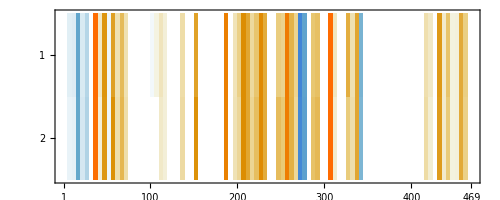

```mathematica
MatrixPlot[{KernelOrigin,insphere[[2]]},ImageSize->Full]
```

The two rows of this matrix are very similar although not identical.
The actual main flux components of this typical flux and the names of reactions they belong to, are as follows:

```mathematica
midrxns=Flatten@Position[KernelOrigin,_?(#>0.1&)];
midflux=Transpose[{Map[ReactionNames[[#]]<>"   "&,midrxns],KernelOrigin[[midrxns]]}];
Multicolumn[midflux,3,Appearance->Horizontal,Alignment->".",Spacings->{1,0}]
```

{EX_h_e   ,8.76378} | {GALKr   ,0.3169} | {ME2   ,0.476109}
{EX_hco3_e   ,5.87112} | {GALt1r   ,0.3169} | {NAt   ,8.80668}
{EX_lac__L_e   ,2.86736} | {GAPD   ,2.92556} | {NaKt   ,2.93556}
{EX_o2_e   ,1.76007} | {GLCt1   ,1.12} | {PFK   ,1.46111}
{EX_pyr_e   ,0.534344} | {GTHOr   ,0.27491} | {PGI   ,1.2357}
{CAT   ,1.76007} | {GTHPi   ,0.237391} | {PGMT   ,0.3169}
{CO2t   ,5.33417} | {H2O2t   ,3.75754} | {PYK   ,2.92556}
{DM_nadh   ,0.259396} | {H2Ot   ,2.08381} | {SBTD_D2   ,0.201199}
{ENO   ,2.92556} | {HCO3E   ,5.87112} | {SBTR   ,0.201199}
{FBA   ,1.46111} | {HEX1   ,0.918801} | {TPI   ,1.46111}
{FUM   ,0.121945} | {HEX7   ,0.208699} | {UGLT   ,0.3169}
{FUMtr   ,0.121945} | {MALt   ,0.354165} |

The second part of the Kernel transform is the set of basis vectors that span the Kernel space, and they were chosen to  point along principal axes of the Kernel space.
As vectors in the full flux space (FFS) they are as follows:

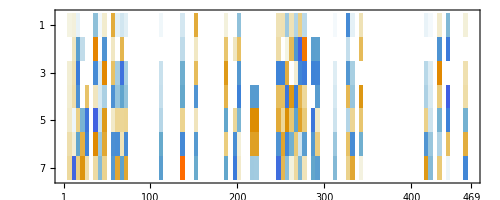

```mathematica
MatrixPlot[KernelBasis,ImageSize->Full]
```

The Kernel space itself is characterised by a set of normalised constraint vectors, specifying constraint hyperplanes by their normal directions:

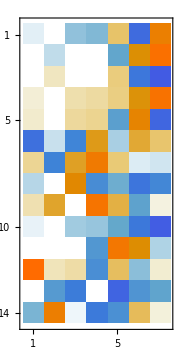

```mathematica
MatrixPlot[Kernelcons,ImageSize->Small]
```

The normal distance from the origin, for each constraint hyperplane, is given by the constraint values that make up the second part of the Kernelspace specification :

```mathematica
Multicolumn[Transpose[{Map[ToString[#]<>"   "&,Range[Length@Kernelvals]],Kernelvals}],3,Appearance->Horizontal,Spacings->{2,0}]
```

{1   ,0.175831} | {6   ,5.13218} | {11   ,0.28698}
{2   ,0.104681} | {7   ,0.779903} | {12   ,12.4213}
{3   ,0.205299} | {8   ,0.593164} | {13   ,0.316749}
{4   ,0.18862} | {9   ,0.573075} | {14   ,2.1118}
{5   ,0.196813} | {10   ,0.118328} |

#### Ray vectors and thin directions

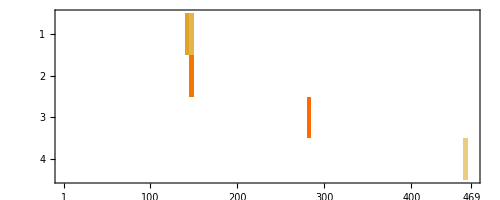

```mathematica
MatrixPlot[rays,ImageSize->Full]
```

The ray vectors form a sparse matrix by construction. The actual reactions that participate in each ray, and their amplitudes, are as follows;

```mathematica
Do[
rr=ArrayRules@SparseArray[rays];
rayrxns=Cases[rr,({ray,rxn_}->ampli_):>{ReactionNames[[rxn]],ampli}];
Print@Multicolumn[Prepend[rayrxns,"Ray no "<>ToString@ray],4,Appearance->Horizontal,Spacings->{3,0}],
{ray,Length@rays}]
```

Ray no 1 | {C160CPT1,0.707107} | {C160CPT2rbc,0.707107} |

Ray no 2 | {C181CPT1,0.707107} | {C181CPT2rbc,0.707107} |

Ray no 3 | {LNLCCPT1,0.707107} | {LNLCCPT2rbc,0.707107} |

Ray no 4 | {GALT,-0.57735} | {GALUi,0.57735} | {UGLT,0.57735}

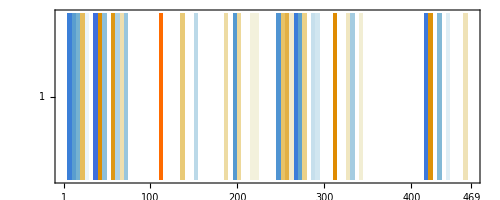

```mathematica
MatrixPlot[thindirs,ImageSize->Full]
```

### Periphery points, and Utilility functions for shifting between Kernel space and Flux space

Express the constraint vectors as vectors in FFS. Then they span the hyperplane which contains the SS Kernel polytope. 
Demonstrate that the thin directions are orthogonal to this hyperplane:

```mathematica
convecs=Kernelcons.KernelBasis;
Chop[convecs.Transpose[thindirs]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

The periphery points are points in FFS, that indicate the range of variation of fluxes that all share the same value for the objective function of the metabolic model.
Demonstrate that they satisfy the Kernel polytpope constraints, i.e. are all feasible:

```mathematica
And@@Map[SolutionTest[#,KernelSpace]=="Full vector in solution space"&,PeriPoints]
```

True

In FFS, where the origin lies at zero flux, the points at the periphery all fall at similar radii, i.e. have similar overall flux, in order to produce the fixed objective values:

```mathematica
Norm/@PeriPoints
```

{28.2561,23.066,23.3343,23.3974,23.7486,23.2888,23.2376,22.5185,23.3384,23.3155,22.8538,23.3534,22.8378,23.2921,23.536,22.8319,22.5966,22.3621,22.7999,22.6162,22.8183,22.7156,22.6615,22.5762,22.7439,22.721,22.6446,22.6868,22.7157,22.7125,22.6245,22.5112,23.3522,23.1113,22.5913,22.3004,22.6341,22.9994,23.1008,22.6159,22.6044,22.8418,22.8638,22.5439,22.5395,22.4889,22.5553,22.7305,22.8726,22.5456,22.7211,22.5621,22.648,22.6717,22.7142,22.6036,22.6326,22.6833,22.6467,22.6285,22.6209,22.6947}

Now use one of the provided utility functions to respecify them relative to the Kernel space origin and in terms of the Kernel space basis.  The respecified vectors would be expected to have quite different lengths.

```mathematica
Dimensions[PeriPoints]
perips=DowncastPoint[PeriPoints,KernelTransform];
Dimensions@perips
```

{62,469}

{62,7}

If these projected points are transferred back to FFS, the original points are recovered (within numerical accuracy). This demonstrates that the original FFS points in fact do fall in the Kernelspace hyperplane, since the projection did not remove any vector components:

```mathematica
difs=UpliftPoint[perips,KernelTransform]-PeriPoints;
Chop[Norm/@difs]
```

{0,0.0000217694,0,4.58641×10^-6,0,7.27513×10^-6,0,0.0000222078,0,0,4.58212×10^-6,0.0000203186,0,0,6.82913×10^-6,0,0,0,0,0,0,0,0,0,0,7.22769×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7.02851×10^-8,0,0,0,0,0,0,0,0,0,0,0,6.24409×10^-6,0,0,0,0,0,0,0,0,0}

Relative to the new origin, they represent varying radii:

```mathematica
Norm/@perips
Min[%]
```

{13.9262,8.74923,7.8447,4.18043,3.9205,4.03169,7.39105,5.91439,4.19998,4.03021,4.21398,7.92172,1.03139,2.91857,3.08142,0.941189,1.22112,0.969743,0.546608,0.573075,0.616672,0.730561,0.35242,0.499429,0.301992,0.364399,0.235423,0.196813,0.235081,0.183933,0.242914,5.17681,3.2076,2.96752,2.62253,2.59513,2.52922,2.43653,2.16831,2.14156,2.06846,1.95151,1.63104,0.971329,0.941829,0.872206,0.779903,0.673505,0.605155,0.530837,0.517623,0.453592,0.372512,0.28698,0.254657,0.244469,0.228598,0.193409,0.175831,0.175397,0.174897,0.170425}

0.170425

Compare the minimal periphery point radius above  with the radius of the maximal inscribed hypersphere:

```mathematica
insphere[[1]]
```

0.153474

The directions of the peripheral points should be roughly uniformly distributed over all directions available in the kernel hyperplane. 
Investigate that by checking the angles between all pairs of points, and comparing that with the single common angle value between any pair of  directions to the equally spaced vertices of a simplex, in the same number of dimensions:

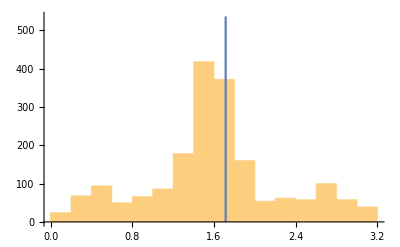

The number of directions exceeds the number of simplex directions by a factor 7.75

```mathematica
directions=Normalize/@perips;
pairangles=Flatten@Table[ArcCos[directions[[i]].directions[[j]]],{i,1,Length@directions-1},{j,i+1,Length@directions}];
Kerneldim=Last@Dimensions[directions];
simplexangle=N@ArcCos[-1/Kerneldim];
simplexline=ListLinePlot[{{simplexangle,0},{simplexangle,Max@BinCounts[pairangles,Pi/Floor[1+Log2[Length@pairangles]]]}}];
Show[Histogram[pairangles],simplexline]
Print["The number of directions exceeds the number of simplex directions by a factor "<>TextString[Length@directions/(Kerneldim+1)]]
```

For a simplex, vertex directions are uniformly spaced and all pair angles are exactly equal. 
For a roughly uniform distribution of directions, the angle between nearest neighbour directions will all be similar so represent the largest group; then a smaller group of  similar values to second nearest neighbours, etc up to a small number of directly opposing directions that give an angle value near 3.14159 radians. There should be few directions with pair angles near zero. 
So the median pair angle should be similar to the simplex value, but somewhat smaller since there are  more directions.

### Periphery points as representative fluxes

While the origin of the Kernel space serves as a single representative flux value, the set of periphery points can be useful to estimate e.g. the mean value of some function of the fluxes, or the range of variation of such a function. 
Demonstrate that idea by simply looking at individual flux values. Only a flux that varies over the Kernelspace is interesting for this, so first determine which ones they are:

```mathematica
fluxdim=Length@KernelOrigin;
varfluxes=Complement[Range[fluxdim],fixvals[[All,1]]]
```

{8,12,13,20,22,27,36,37,38,42,46,50,57,60,65,69,75,113,114,137,138,140,145,146,147,148,152,186,200,201,220,221,226,227,248,249,251,257,258,263,266,270,271,276,277,281,282,288,293,314,328,332,341,419,420,422,433,442,443,461,465}

The identifiers and  range of variation of the variable fluxes, over the periphery points are

```mathematica
Multicolumn[Map[{ReactionNames[[#]]<>"   ",Min[PeriPoints[[All,#]]],Max[PeriPoints[[All,#]]]}&,varfluxes],
2,Appearance->Horizontal,Spacings->{4,0}]
```

{EX_ade_e   ,-0.014,0.01} | {FUMtr   ,-0.5,0.25}
{EX_arg__L_e   ,-0.1152,0} | {GALT   ,0,0}
{EX_ascb__L_e   ,0,0.1111} | {GALUi   ,0,0}
{EX_co2_e   ,-5.87112,-5.00592} | {GTHDH   ,0,0.1111}
{EX_dhdascb_e   ,-0.1111,0} | {GTHOr   ,0,0.75}
{EX_fum_e   ,-0.25,0.5} | {GTHPi   ,0,0.75}
{EX_h_e   ,8.03236,10.} | {H2O2t   ,0,10.}
{EX_h2o_e   ,-6.14246,4.30148} | {H2Ot   ,-4.30148,6.14246}
{EX_h2o2_e   ,-10.,0} | {HEX1   ,0.37,1.12}
{EX_hxan_e   ,0,0.024} | {HEX7   ,0.0075,0.7575}
{EX_lac__L_e   ,1.8793,3.67556} | {HYXNt   ,-0.024,0}
{EX_mal__L_e   ,-0.5,0.161058} | {Ht   ,-6.52656,-4.37113}
{EX_nh4_e   ,0,0.0240474} | {L_LACt2r   ,-3.67556,-1.8793}
{EX_o2_e   ,0,4.71406} | {LDH_L   ,-3.67556,-1.8793}
{EX_ptrc_e   ,0,0.1152} | {LNLCCPT1   ,0,0}
{EX_pyr_e   ,0,1.7963} | {LNLCCPT2rbc   ,0,0}
{EX_urea_e   ,0,0.1152} | {MALt   ,-0.161058,0.5}
{ADA   ,0,0.024} | {ME2   ,0,0.75}
{ADEt   ,-0.01,0.014} | {NH4t3r   ,0,0.0240474}
{ARGN   ,0,0.1152} | {O2t   ,-4.71406,0}
{ARGt5r   ,0,0.1152} | {ORNDC   ,0,0.1152}
{ASCBt   ,-0.1111,0} | {PGI   ,0.6869,1.4369}
{C160CPT1   ,0,0} | {PTRCtex2   ,0,0.1152}
{C160CPT2rbc   ,0,0} | {PUNP1   ,-0.014,0.01}
{C181CPT1   ,0,0} | {PUNP5   ,0,0.024}
{C181CPT2rbc   ,0,0} | {PYRt2   ,-1.7963,0}
{CAT   ,0,4.71406} | {SBTD_D2   ,0,0.75}
{CO2t   ,5.00592,5.87112} | {SBTR   ,0,0.75}
{DHAAt1r   ,0,0.1111} | {UGLT   ,0.3169,0.3169}
{DM_nadh   ,0,1.04626} | {UREAt   ,-0.1152,0}
{FUM   ,-0.5,0.25} |

These ranges are generally expected to be smaller than those obtained from a Flux Variability (FVA) calculation for the same model, because they only describe variation over a typical “central” part of the Kernelspace.

As an example of averaging, calculate the mean value of each variable flux over  all periphery points, compared with its value at the centre point:

```mathematica
Multicolumn[Map[{ReactionNames[[#]]<>"   ",Mean[PeriPoints[[All,#]]],KernelOrigin[[#]]}&,varfluxes],
2,Appearance->Horizontal,Spacings->{4,0}]
```

{EX_ade_e   ,-0.00489093,-0.00474803} | {FUMtr   ,0.121469,0.121945}
{EX_arg__L_e   ,-0.0608021,-0.0608433} | {GALT   ,0,0}
{EX_ascb__L_e   ,0.0386167,0.0375188} | {GALUi   ,0,0}
{EX_co2_e   ,-5.33553,-5.33417} | {GTHDH   ,0.0386167,0.0375188}
{EX_dhdascb_e   ,-0.0386167,-0.0375188} | {GTHOr   ,0.273731,0.27491}
{EX_fum_e   ,-0.121469,-0.121945} | {GTHPi   ,0.235114,0.237391}
{EX_h_e   ,8.76158,8.76378} | {H2O2t   ,3.74673,3.75754}
{EX_h2o_e   ,-2.09652,-2.08381} | {H2Ot   ,2.09652,2.08381}
{EX_h2o2_e   ,-3.74673,-3.75754} | {HEX1   ,0.918937,0.918801}
{EX_hxan_e   ,0.0148916,0.014748} | {HEX7   ,0.208563,0.208699}
{EX_lac__L_e   ,2.86893,2.86736} | {HYXNt   ,-0.0148916,-0.014748}
{EX_mal__L_e   ,-0.353325,-0.354165} | {Ht   ,-5.37613,-5.37686}
{EX_nh4_e   ,0.0149351,0.0147954} | {L_LACt2r   ,-2.86893,-2.86736}
{EX_o2_e   ,1.75581,1.76007} | {LDH_L   ,-2.86893,-2.86736}
{EX_ptrc_e   ,0.0608021,0.0608433} | {LNLCCPT1   ,0,0}
{EX_pyr_e   ,0.53146,0.534344} | {LNLCCPT2rbc   ,0,0}
{EX_urea_e   ,0.0608021,0.0608433} | {MALt   ,0.353325,0.354165}
{ADA   ,0.0148916,0.014748} | {ME2   ,0.474794,0.476109}
{ADEt   ,0.00489093,0.00474803} | {NH4t3r   ,0.0149351,0.0147954}
{ARGN   ,0.0608021,0.0608433} | {O2t   ,-1.75581,-1.76007}
{ARGt5r   ,0.0608021,0.0608433} | {ORNDC   ,0.0608021,0.0608433}
{ASCBt   ,-0.0386167,-0.0375188} | {PGI   ,1.23584,1.2357}
{C160CPT1   ,0,0} | {PTRCtex2   ,0.0608021,0.0608433}
{C160CPT2rbc   ,0,0} | {PUNP1   ,-0.00489093,-0.00474803}
{C181CPT1   ,0,0} | {PUNP5   ,0.0148916,0.014748}
{C181CPT2rbc   ,0,0} | {PYRt2   ,-0.53146,-0.534344}
{CAT   ,1.75581,1.76007} | {SBTD_D2   ,0.201063,0.201199}
{CO2t   ,5.33553,5.33417} | {SBTR   ,0.201063,0.201199}
{DHAAt1r   ,0.0386167,0.0375188} | {UGLT   ,0.3169,0.3169}
{DM_nadh   ,0.257694,0.259396} | {UREAt   ,-0.0608021,-0.0608433}
{FUM   ,0.121469,0.121945} |

The values closely agree in this case, because the Kernel origin was taken as the centroid of the periphery points. The same should apply for any linear function of fluxes, but for nonlinear functions averaging the periphery points should give a different value.